```mathematica
x=3
```

3

```mathematica
y=4;
```

```mathematica
z=x+y
```

7

```mathematica
f=5/2+2*t
```

5/2+2 t

```mathematica
f=2.5+2*t
```

2.5+2 t

```mathematica
(*here is a comment*)
dog = 4;
cat =5/u+6.5;
(*bala ba*)
goat=dog+cat+750
```

760.5+5/u

Section 1: Basics
hello world! text cell here.
h=6*goat;

## Section 2 : new section

```mathematica
hh=9
```

9

## Greek symbols

x^2=0

Set::write: Tag Power in 3^2 is Protected.

0

αx^2+xβ+γ=0

Set::write: Tag Plus in xβ+αx^2+γ is Protected.

0

```mathematica
x
y
f
β
```

3

4

2.5+2 t

β

```mathematica
Clear[x]
```

```mathematica
Sin[π]
```

0

```mathematica
Sin[45*π/180]
```

1/(√2)

```mathematica
Sin[45.0*π/180]
```

0.707107

```mathematica
Solve[a x^2+b x +c==0, x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

## 2D Plot

### plot

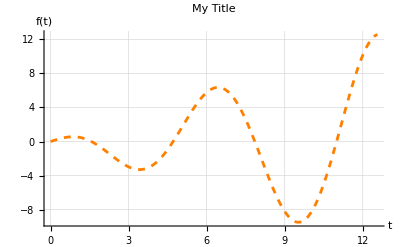

```mathematica
Plot[t*Cos[t],{t, 0,4 π},
(*options*)
 AxesLabel->{"t","f(t)" },
PlotLabel->"My Title",
GridLines->Automatic,
PlotStyle->{Orange,Dashed,Thickness[0.005]},
PlotRange->All]
```

multiple functions to same axes

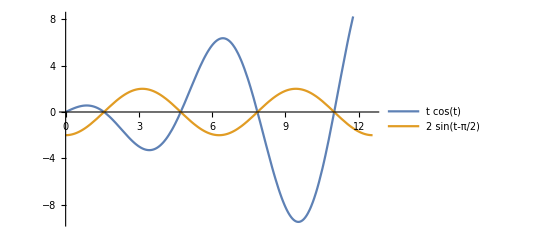

```mathematica
Plot[{t*Cos[t],2 Sin[t-π/2]},{t, 0,4 π},
PlotLegends->"Expressions"]
```

## Show

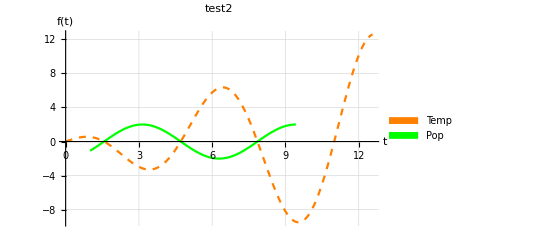

```mathematica
plot1 = Plot[t*Cos[t],{t, 0,4 π},
PlotStyle->{Orange,Dashed}];

plot2= Plot[2 Sin[t-π/2],{t, 1,3 π},
PlotStyle->Green];

Legended[Show[plot1,plot2,
(*Options*)
PlotLabel-> "test2",
AxesLabel-> {"t","f(t)"},
PlotRange-> All,
GridLines->Automatic],
(*legend*)
SwatchLegend[{Orange,Green},{"Temp", "Pop"}]]
```

## ListPlot

(1 | 2)

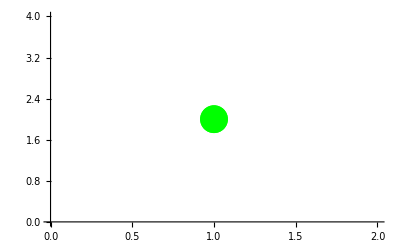

```mathematica
pt1={{1,2}};
pt1 //MatrixForm
ListPlot[pt1,
PlotStyle->{Green, PointSize[0.05]}
]
```

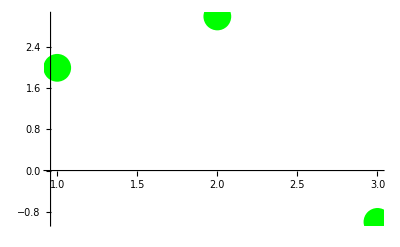

```mathematica
points =({{1, 2}, {2, 3}, {3, -1}});
plotA = ListPlot[points,
PlotStyle->{Green, PointSize[0.05]}
]
```

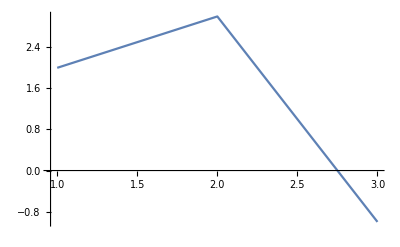

-Graphics-

```mathematica
plotB=ListLinePlot[points]
```

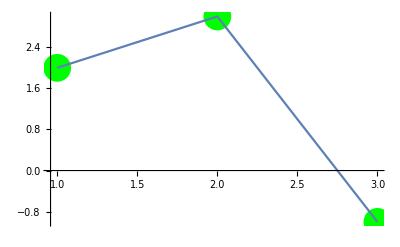

```mathematica
Show[plotA,plotB]
```

fake data

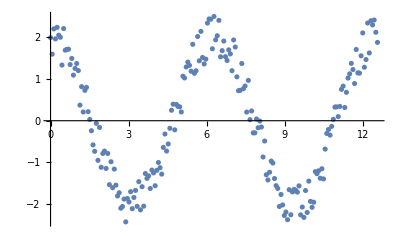

```mathematica
data = Table[{t,2 Cos[t]+RandomReal[]-0.5},{t,0,4 π,2π/100}];
dataPlot=ListPlot[data]
```

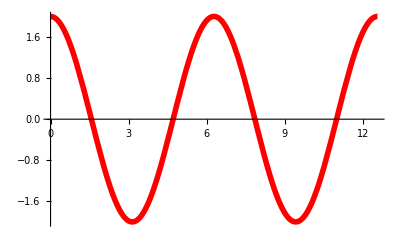

```mathematica
fitPlot=Plot[2 Cos[t],{t,0,4 π},
PlotStyle->{Red,Thickness[0.01]}]
```

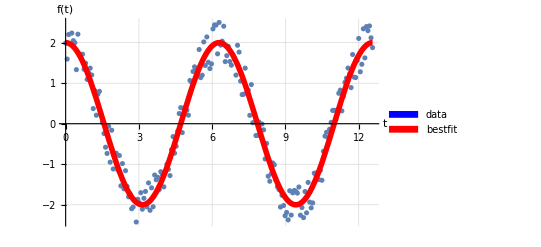

```mathematica
Legended[Show[dataPlot, fitPlot,
AxesLabel-> {"t","f(t)"},
GridLines->Automatic],
SwatchLegend[{Blue,Red},{"data","bestfit"}]]
```

## DiscretPlot

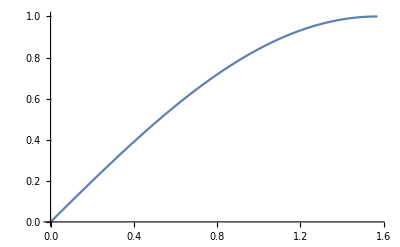

```mathematica
Plot[Sin[x],{x,0,π /2}]
```

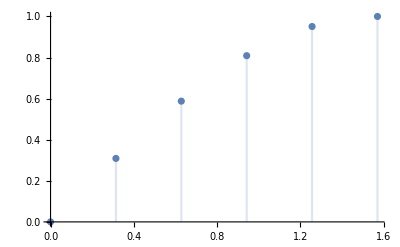

```mathematica
DiscretePlot[Sin[x],{x,0,π /2,10 π/100}]
```

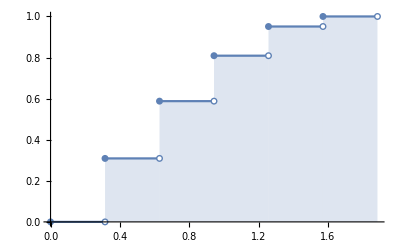

```mathematica
DiscretePlot[Sin[x],{x,0,π /2,10 π/100},
ExtentSize->Right,
ExtentMarkers->{"Filled","Empty"}]
```

## Histogram

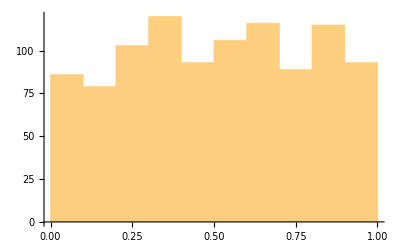

```mathematica
data2 = Table[RandomReal[],{i,1,1000}];
data2//MatrixForm;

Histogram[data2]
```

## PieChart

```mathematica
PieChart[{2,5,9}]
```

-Graphics-

## 3DPlot Surfaces

```mathematica
plotsurface=Plot3D[Cos[x1]*x2,{x1,-π,π},{x2,-10,16}]
```

-Graphics3D-

```mathematica
Plot3D[Cos[x1]*x2,{x1,-π,π},{x2,-10,16},
AxesLabel->{"x1","x2","f(x1,x2)"},
PlotLabel->"f=coa(x1)x2",
ColorFunction->"Rainbow",
FaceGrids->All]
```

-Graphics3D-

```mathematica
Plot3D[Cos[x1]*x2,{x1,-π,π},{x2,-10,16},
ViewPoint->Front]
```

-Graphics3D-

```mathematica
Plot3D[Cos[x1]*x2,{x1,-π,π},{x2,-10,16},
ViewPoint->{0,-∞,0}]
```

-Graphics3D-

## 3DLines

```mathematica
plotline=ParametricPlot3D[{t,4t-2,Cos[t]*(4t-2)},{t,-2,2},
AxesLabel->{"x","y","z"},
PlotStyle->{Red,Thickness[0.02]}]
```

-Graphics3D-

```mathematica
Show[plotsurface,plotline]
```

-Graphics3D-

## Points in 3D

```mathematica
p=({{-2, 3, Cos[-2]+3}});
p//MatrixForm

pt=Point[p];
plotpoint=Graphics3D[{AbsolutePointSize[15], Green,pt}]
```

(-2 | 3 | 3+Cos[2])

-Graphics3D-

```mathematica
Show[plotsurface,plotline,plotpoint]
```

-Graphics3D-

## Matrices

```mathematica
x=3;
y=2;
z=t^2;
```

```mathematica
a = {1,2}
b={3,4,z}
```

{1,2}

{3,4,t^2}

### Define

```mathematica
A={{1,2},{3,4},{5,6}}
```

{{1,2},{3,4},{5,6}}

```mathematica
MatrixForm[A]
A//MatrixForm
```

(1 | 2
3 | 4
5 | 6)

(1 | 2
3 | 4
5 | 6)

```mathematica
B3={{4,5},{5,6},{t,t^3}}
B3//MatrixForm
```

{{4,5},{5,6},{t,t^3}}

(4 | 5
5 | 6
t | t^3)

```mathematica
A+B3 //MatrixForm
```

(5 | 7
8 | 10
5+t | 6+t^3)

ctrl+enter   add rows
ctrl+,   add cols

### Multply

```mathematica
A=({{1, 2, 4}, {-3, 3, 4.5}});
B=({{1, 2, 3}, {2, 6, 5}, {9, 8, 4}});
AB=Dot[A,B];
AB//MatrixForm
AB=A.B;
AB//MatrixForm
```

(41. | 46. | 29.
43.5 | 48. | 24.)

(41. | 46. | 29.
43.5 | 48. | 24.)

### Elementwise multiplication

```mathematica
A=({{1, 2, 3}, {6, 2, 3}});
B=({{5, 3, 2}, {8, 3, 1}});
AB=A+B;
AB//MatrixForm
```

(6 | 5 | 5
14 | 5 | 4)

Thread::tdlen: Objects of unequal length in {{1, 2, 4}, {-3, 3, 4.5}} + {{1, 2, 3}, {2, 6, 5}, {9, 8, 4}} cannot be combined.

### Power

```mathematica
A=({{1, 2}, {4, 3}})
A^2 //MatrixForm
A.A //MatrixForm
```

{{1,2},{4,3}}

(1 | 4
16 | 9)

(9 | 8
16 | 17)

```mathematica
MatrixPower[A,2]//MatrixForm
```

(9 | 8
16 | 17)

```mathematica
Part[A,2,1]
```

4

```mathematica
A[[2,1]]
```

4

```mathematica
row2 = {A[[2,All]]}
row2  //MatrixForm
```

{{4,3}}

(4 | 3)

### Transpose

```mathematica
clo2 = Transpose[{A[[All,2]]}];
clo2//MatrixForm
```

(2
3)

### Concat

```mathematica
r1 = ({{1, 2, 3}});
r2 = ({{3, 4, 5}});

A = Join[r1,r2];
A//MatrixForm
```

(1 | 2 | 3
3 | 4 | 5)

```mathematica
c1=({{3}, {2}, {5}});
c2=({{5}, {6}, {7}});

Transpose[Join[Transpose[c1],Transpose[c2]]]//MatrixForm
```

(3 | 5
2 | 6
5 | 7)